# Σ2 (p=0, ω)

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx
```

## Integrand

```mathematica
f[ q1_, q2_, ω_, ω1_, ω2_,costheta_, ε1_ , ε2_]:=-4*Pi/(2*Pi)^8*q1^2*2*Pi* q2^2* vq2[q1]*vq2[q2]*dqw[q1,ω1,ε1]*dqw[q2,ω2,ε2]*(g0pw[q1, ω-ω1,ε1])^2*g0pwcos[q1,q2, ω-ω1-ω2,costheta,ε2]*Exp[ⅈ*ω1*ε1]*Exp[ⅈ*ω2*ε2]
```

## ω2 Integral

### Cauchy Principle value

```mathematica
Limit[Integrate[f[ q1,q2, ω, ω1,ω2,ct, ε1, ε2 ],{ω2, -Infinity,Infinity}, PrincipalValue->true, Assumptions->ε>0 ], ε -> 0]
```

$Aborted

### Residuensatz

```mathematica
w2pol := ω2/.Solve[Denominator[f[ q1,q2, ω, ω1,ω2,costheta, ε1, ε2 ]]==0,ω2];
```

```mathematica
Limit[2*Pi*Residue[f[ q1,q2, ω, ω1,ω2,costheta, ε1, ε2 ], {ω2, w2pol[[2]]}, Assumptions->ε1>0 && ε2>0],ε2->0]
```

(4.64422 2.71828^((0.+1. ⅈ) ε1 ω1) q1^2 √(q1^2/(2+q1^2)) q2^2 √(q2^2/(2+q2^2)))/((√(q1^2 (2+q1^2))-(0.+2. ⅈ) ε1-2. ω1) (4.+1. q1^2+2. costheta q1 q2+1. q2^2+1. √(q2^2 (2.+q2^2))-2. ω+2. ω1) (4.+q1^2-(0.+2. ⅈ) ε1-2. ω+2. ω1)^2)

```mathematica
g[q1_, q2_, ω_, ω1_,costheta_, ε1_ ]:=(4.64421801704243 2.718281828459045^((0.+1. ⅈ) ε1 ω1) q1^2 √(q1^2/(2+q1^2)) q2^2 √(q2^2/(2+q2^2)))/((√(q1^2 (2+q1^2))-(0.+2. ⅈ) ε1-2. ω1) (4.+1. q1^2+2. costheta q1 q2+1. q2^2+1. √(q2^2 (2.+q2^2))-2. ω+2. ω1) (4.+q1^2-(0.+2. ⅈ) ε1-2. ω+2. ω1)^2)
```

## ω1 Integral

### Residuensatz

```mathematica
w1pol = ω1/.Solve[Denominator[g[ q1,q2, ω, ω1,costheta, ε1 ]]==0,ω1]
```

{0.5 (√(2. q1^2+q1^4)-(0.+2. ⅈ) ε1),-2.-0.5 q1^2-1. costheta q1 q2-0.5 q2^2-0.5 √(2. q2^2+q2^4)+1. ω,-2.-0.5 q1^2+(0.+1. ⅈ) ε1+1. ω,-2.-0.5 q1^2+(0.+1. ⅈ) ε1+1. ω}

```mathematica
Sum[Limit[2*Pi*Residue[g[ q1,q2, ω, ω1,costheta, ε1 ], {ω1, w1pol[[i]]}, Assumptions->ε1>0 ],ε1->0],{i,2,3,1}]
```

(14.5902 q1^2 √(q1^2/(2+q1^2)) q2^2 √(q2^2/(2+q2^2)))/((2. costheta q1 q2+1. q2^2+1. √(2. q2^2+q2^4))^2 (4.+1. q1^2+1. √(q1^2 (2.+q1^2))+2. costheta q1 q2+1. q2^2+1. √(2. q2^2+q2^4)-2. ω))+((14.5902+0. ⅈ) q1^2 √(q1^2/(2+q1^2)) q2^2 √(q2^2/(2+q2^2)) (-4.-1. q1^2-1. √(q1^2 (2.+q1^2))+2. costheta q1 q2+1. q2^2+1. √(2. q2^2+q2^4)+2. ω))/((2. costheta q1 q2+1. q2^2+1. √(2. q2^2+q2^4))^2 (4.+1. q1^2+1. √(q1^2 (2.+q1^2))-2. ω)^2)

```mathematica
h[ q1_, q2_, ω_, costheta_ ]:=(14.590241204009855 q1^2 √(q1^2/(2+q1^2)) q2^2 √(q2^2/(2+q2^2)))/((2. costheta q1 q2+1. q2^2+1. √(2. q2^2+q2^4))^2 (4.+1. q1^2+1. √(q1^2 (2.+q1^2))+2. costheta q1 q2+1. q2^2+1. √(2. q2^2+q2^4)-2. ω))+((14.590241204009855+0. ⅈ) q1^2 √(q1^2/(2+q1^2)) q2^2 √(q2^2/(2+q2^2)) (-4.-1. q1^2-1. √(q1^2 (2.+q1^2))+2. costheta q1 q2+1. q2^2+1. √(2. q2^2+q2^4)+2. ω))/((2. costheta q1 q2+1. q2^2+1. √(2. q2^2+q2^4))^2 (4.+1. q1^2+1. √(q1^2 (2.+q1^2))-2. ω)^2)
```

## Σ2 with NIntegrate

```mathematica
Σ2[ω_]:=NIntegrate[h[q1,q2, ω, costheta],{q1,0, qc},{q2,0, qc},{costheta,-1, 1}];
```

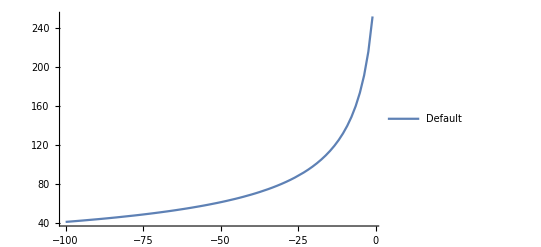

```mathematica
Plot[Σ2[w],{w,-100,-1},PlotPoints->10,MaxRecursion ->3,PlotRange->Full, PlotLegends-> {"Default"}]
```

```mathematica
Σ2omegadata= Table[{ω,Σ2[ω]},{ω, -100, 2, 1}];
```

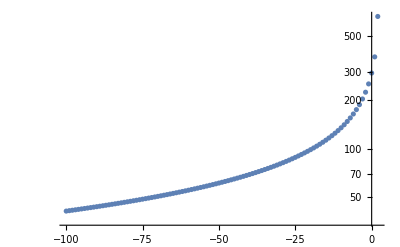

```mathematica
Σ2wplot = ListLogPlot[Σ2omegadata]
```

```mathematica
DumpSave["2nd_SEw.mx",{Σ2wplot, Σ2omegadata}];
Export["mat_2nd_sew", Σ2omegadata, "Table"];
```